```mathematica
Q. 8(a)
```

```mathematica
eqn=y'[t]==t*Exp[3 t]-2*y[t];
ic=y[0]==0;

sol=DSolve[{eqn,ic},y[t],t];
exactSol[t_]=y[t]/. sol[[1]];

Print["Exact Solution:"];
exactSol[t]//Simplify;

Plot[exactSol[t],{t,0,1},PlotLabel->"Exact Solution for y(t)"]
```

Exact Solution:

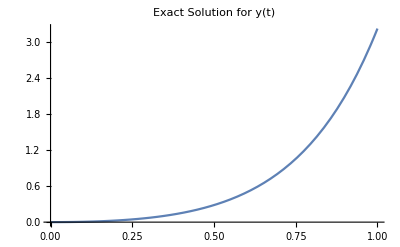

```mathematica
Q. 8 (a)
```

```mathematica
sol
```

{{y[t]→1/25 ⅇ^(-2 t) (1-ⅇ^(5 t)+5 ⅇ^(5 t) t)}}

```mathematica
Q. 8 (b)

eqn=y'[t]==1-(t-y[t])^2;
ic=y[2]==1;

sol=DSolve[{eqn,ic},y[t],t];

exactSol[t_]=y[t]/. sol[[1]];

Print["Exact Solution:"];
exactSol[t]//Simplify;

Plot[exactSol[t],{t,2,3},PlotLabel->"Exact Solution for y(t)"]
```

Exact Solution:

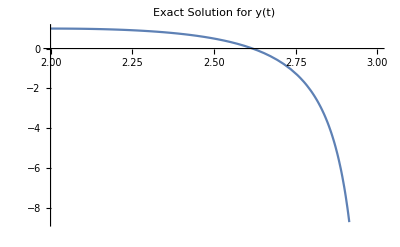

```mathematica
Q.8 (b)
```

```mathematica
sol
```

{{y[t]→(1-3 t+t^2)/(-3+t)}}

```mathematica
Q. 8 (c)
eqn=y'[t]==1+y[t]/t;
ic=y[1]==2;

sol=DSolve[{eqn,ic},y[t],t];

exactSol[t_]=y[t]/. sol[[1]];

Print["Exact Solution:"];
exactSol[t]//Simplify;

Plot[exactSol[t],{t,1,2},PlotLabel->"Exact Solution for y(t)"]
```

Exact Solution:

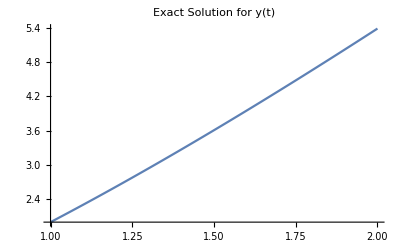

```mathematica
Q. 8 (c)
```

```mathematica
sol
```

{{y[t]→2 t+t Log[t]}}

```mathematica
Q. 8 (d)
```

```mathematica
eqn=y'[t]==Cos[2 t]+Sin[3 t];
ic=y[0]==1;

sol=DSolve[{eqn,ic},y[t],t];

exactSol[t_]=y[t]/. sol[[1]];

Print["Exact Solution:"];
exactSol[t]//Simplify;

Plot[exactSol[t],{t,0,1},PlotLabel->"Exact Solution for y(t)"]
```

Exact Solution:

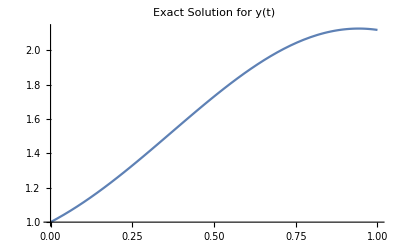

```mathematica
Q. 8 (d)
```

```mathematica
sol
```

{{y[t]→1/6 (8-2 Cos[3 t]+3 Sin[2 t])}}